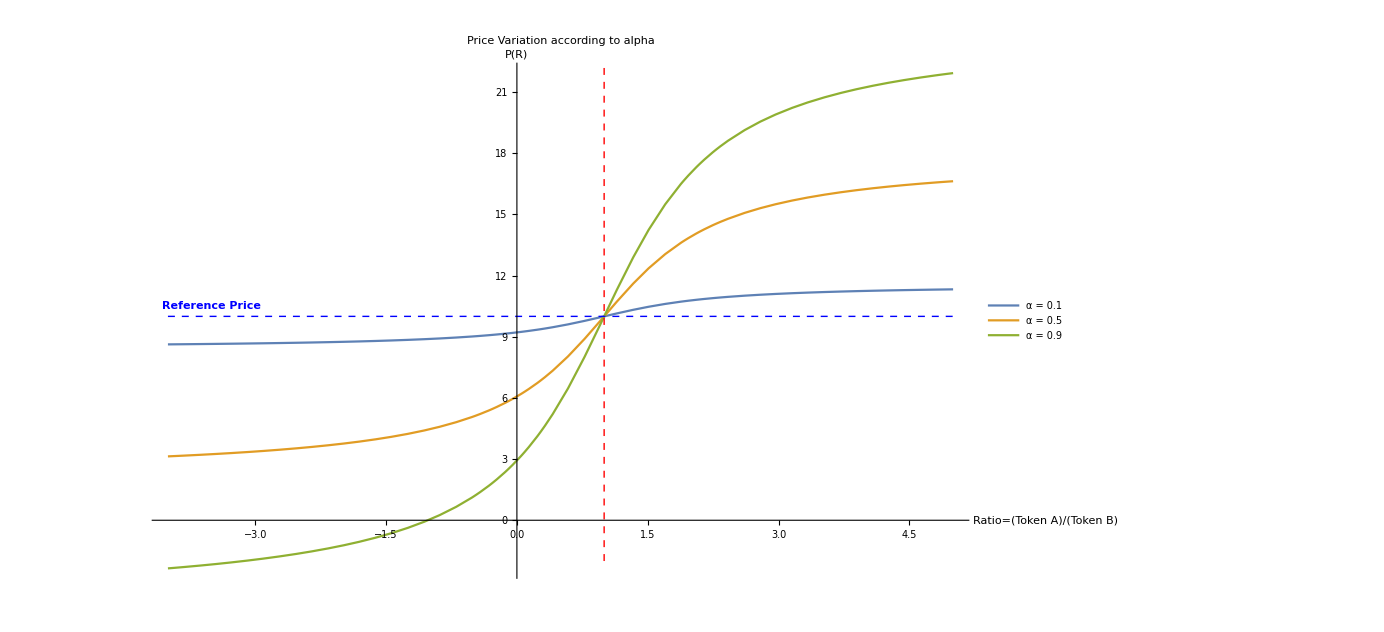

```mathematica
(*Definir la función P*)P[R_,PRef_,α_,β_]:=PRef*(1+α*ArcTan[β*(R-1)])

(*Graficar tres casos con diferentes valores de alpha,ajustando el tamaño de la imagen*)
Plot[{P[R,10,0.1,1],P[R,10,0.5,1],P[R,10,0.9,1]},{R,-4,5},PlotLabel->"Price Variation according to alpha",(*Título en inglés*)PlotLegends->{"α = 0.1","α = 0.5","α = 0.9"},AxesLabel->{"Ratio=(Token A)/(Token B)","P(R)"},Epilog->{(*Línea vertical en R=1 con etiqueta*)Red,Dashed,Line[{{1,-2},{1,25}}],Text[Style["Ratio Token A vs Token B",Red,Bold],{1.7,23}],(*Línea horizontal en PRef=10 con etiqueta*)Blue,Dashed,Line[{{-4,10},{5,10}}],Text[Style["Reference Price",Blue,Bold],{-3.5,10.5}]},ImageSize->1024 (*Ajustar el tamaño de la imagen*)]
```

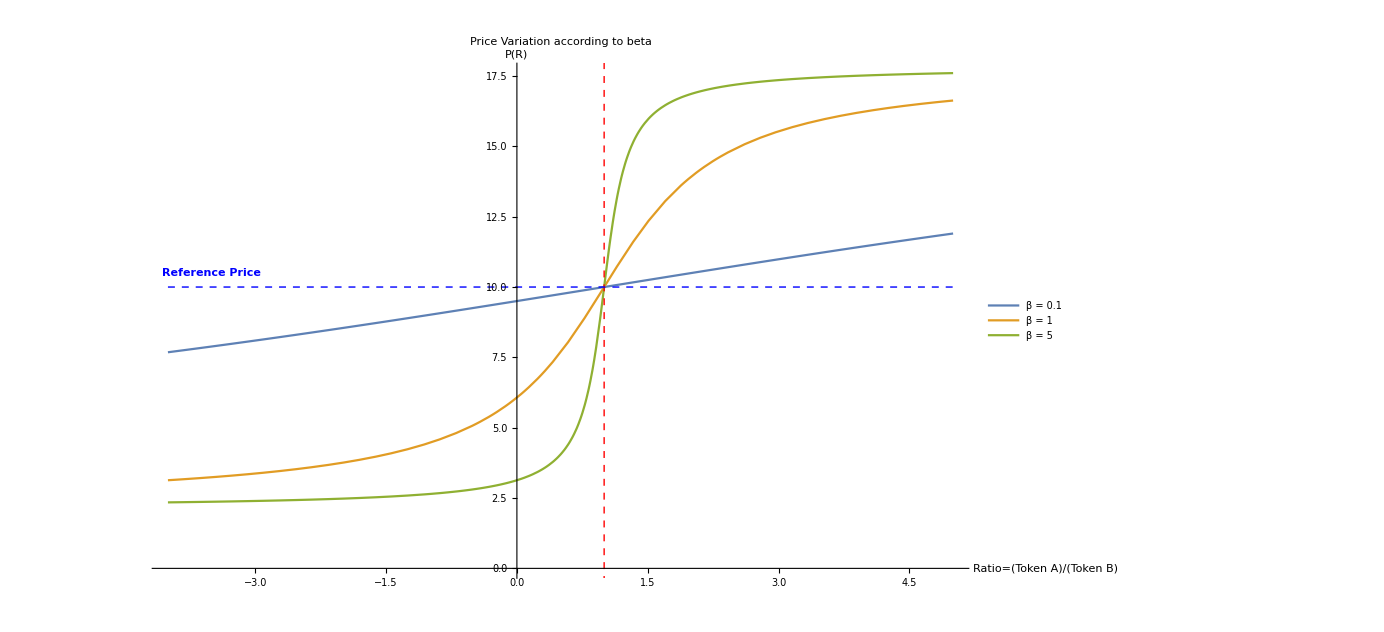

```mathematica
(*Definir la función P*)P[R_,PRef_,α_,β_]:=PRef*(1+α*ArcTan[β*(R-1)])

(*Graficar tres casos con diferentes valores de beta,ajustando el tamaño de la imagen*)
Plot[{P[R,10,0.5,0.1],P[R,10,0.5,1],P[R,10,0.5,5]},{R,-4,5},PlotLabel->"Price Variation according to beta",(*Título en inglés*)PlotLegends->{"β = 0.1","β = 1","β = 5"},AxesLabel->{"Ratio=\!\(\*FractionBox[\(Token\\\ A\), \(Token\\\ B\)]\)","P(R)"},Epilog->{(*Línea vertical en R=1 con etiqueta*)
Red,Dashed,Line[{{1,-2},{1,25}}],Text[Style["Ratio Token A vs Token B",Red,Bold],{1.7,18}],(*Línea horizontal en PRef=10 con etiqueta*)Blue,Dashed,Line[{{-4,10},{5,10}}],Text[Style["Reference Price",Blue,Bold],{-3.5,10.5}]},ImageSize->1024 (*Ajustar el tamaño de la imagen*)]
```